# Probe of the Zγ parameter space (with mixing)

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

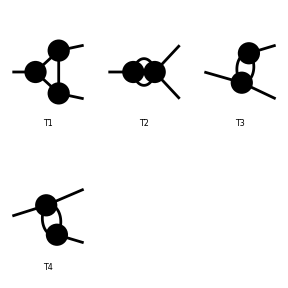

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

Excluding 0 Generic, 31 Classes, and 72 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 8 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 31 Classes, and 72 Particles fields

Restoring 18 field point(s)

in total: 12 Particles insertions

> Top. 1 ad/becf/dedfef.m, 8 diagrams

> Top. 2 ad/bece/dede.m, 4 diagrams

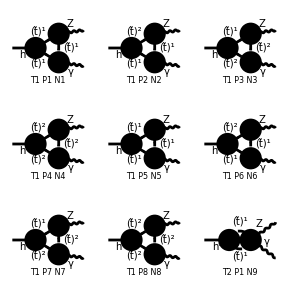

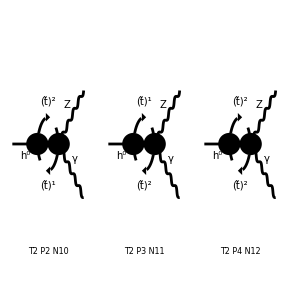

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[2],V[1]},InsertionLevel->{Particles},Model->"MSSM",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[OffShell[CreateFeynAmp[diag1],2-> mg1,3-> mg2],FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 8 Particles amplitudes

> Top. 2: 4 Particles amplitudes

in total: 12 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[2],k[2],mg1,{}},{V[1],k[3],mg2,{}}}][-1/(36 CW2 MW π SB SW2)Alfa EL (Pair1 (Sub11 Sub7 B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]+(Sub12 Sub13+Sub14 Sub15) B0i[bb0,Mh02,MSf2[1,3,3],MSf2[2,3,3]]+Sub1 Sub6 B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]-4 Sub11 Sub7 C0i[cc00,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]-4 Sub1 Sub6 C0i[cc00,mg1^2,mg2^2,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]])-2 (Sub12 Sub13+Sub14 Sub15) (Pair1 C0i[cc00,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[2,3,3],MSf2[2,3,3]]+Pair1 C0i[cc00,mg2^2,Mh02,mg1^2,MSf2[1,3,3],MSf2[1,3,3],MSf2[2,3,3]]-Pair2 Pair3 C0i[cc12,mg2^2,Mh02,mg1^2,MSf2[1,3,3],MSf2[1,3,3],MSf2[2,3,3]])+2 Pair2 Pair3 (-2 Sub11 Sub7 (C0i[cc12,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])-(Sub12 Sub13+Sub14 Sub15) (C0i[cc12,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,mg1^2,mg2^2,Mh02,MSf2[1,3,3],MSf2[2,3,3],MSf2[2,3,3]])-2 Sub1 Sub6 (C0i[cc12,mg1^2,mg2^2,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,mg1^2,mg2^2,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,mg1^2,mg2^2,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]])))]

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[2],k[2],mg1,{}},{V[1],k[3],mg2,{}}}][0]

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

mat= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-4.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
(*mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify*)
Install["LoopTools"]
```

LinkObject[…]

```mathematica
PrependTo[CurrentValue[$FrontEndSession,"NotebookPath"],NotebookDirectory[]];
```

```mathematica
MixedEvalTester[maxSM_,muMass_,betaAng_]:= {VariableValueGeneratro[maxSM,muMass,betaAng],NotebookEvaluate["simZGammaMix.nb",EvaluationElements->All]}
VariableValueGeneratro[maxSM_,muMass_,betaAng_] :={stopM2 = RandomReal[{75,maxSM}],stopM1 = RandomReal[{75,stopM2}],offM1 = RandomReal[125], offM2=RandomReal[(125 - offM1)],mixT =  RandomReal[{-((stopM2^2 -stopM1^2)/(2*173)),((stopM2^2 -stopM1^2)/(2*173))}],muM = muMass,betaA = betaAng}
```

```mathematica
titleLine = "Run  SMass1  SMass2  Mixing  IMass1  IMass2  NLO Result  Full Result" ;
titleLine >>"paramProbeResults.txt"
titleLine >>"paramProbeBadResults.txt"
titleLine >>"paramProbeHorribleResults.txt"
badCount = 0;
horribleCount =0;
```

```mathematica
AbsoluteTiming[For[i=1 , i < 11, i++,MixedEvalTester[1000,250,1.47];dataLine = " " <>ToString[i]<>" "<>ToString[stopM1]<>" " <>ToString[stopM2]<>" "<>ToString[mixT]<>" "<>ToString[offM1]<> " "<>ToString[offM2]<> " "<> ToString[loResult]<> " " <> ToString[fullResult];PutAppend[dataLine,"paramProbeResults.txt"]; If[fullResult > 1.05 || fullResult<.95,PutAppend[dataLine,"paramProbeBadResults.txt"];badCount++];If[fullResult>2||fullResult<0.5,PutAppend[dataLine,"paramProbeHorribleResults.txt"];horribleCount++]]] (*Max stop mass, mu mass, beta angle*)
```

1

2

3

4

5

6

7

8

9

10

{40.3984,Null}

```mathematica
badCount
```

0

```mathematica
horribleCount
```

0

```mathematica
Print[badCount/(i-1)];Print[horribleCount/(i-1)];
```

0

0